```mathematica
five=Keys[allGraphs3];Length[five]
```

15

```mathematica
fiveSorted=Sort[five,Length[ListofVars[allGraphs3[#1,"colofour"]]]>Length[ListofVars[allGraphs3[#2,"colofour"]]]&];
```

```mathematica
fiveEdges=Block[{i,j, main,mainVars, sub,subVars,result={}},
Monitor[
For[i=1,i≤Length[fiveSorted],i++,
main=fiveSorted[[i]];
mainVars=ListofVars[allGraphs3[main,"colofour"]];
For[j=i+1,j≤Length[fiveSorted],j++,
sub=fiveSorted[[j]];
subVars=ListofVars[allGraphs3[sub,"colofour"]];
If[SubSetQ[mainVars,subVars],
AppendTo[result,main->sub]
]
]
],
{i,j,Length[result]}
];
result
];
```

```mathematica
gCleaned=Block[{g=Graph[fiveEdges],vertices,paths,cleaned=0},
vertices=Sort[VertexList[g]];
Monitor[
Table[
paths=FindPath[g,e[[1]],e[[2]],{2,100}];
If[Length[paths]≠0,
g=EdgeDelete[g,e];
cleaned++
]
,{e,Sort[fiveEdges]}
],
{e,cleaned}
];
Print[cleaned];
g
];
```

17

```mathematica
EdgeCount[gCleaned]
```

24

```mathematica
Length[fiveEdges]
```

41

FindPath::inv: The argument 81 in FindPath[Graph[<15>, <41>], 0, 81] is not a valid vertex.

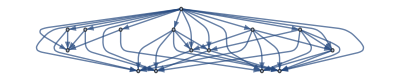
FindPath[-Graphics-,0,81]

```mathematica
FindPath[Graph[fiveEdges],0,81]
```

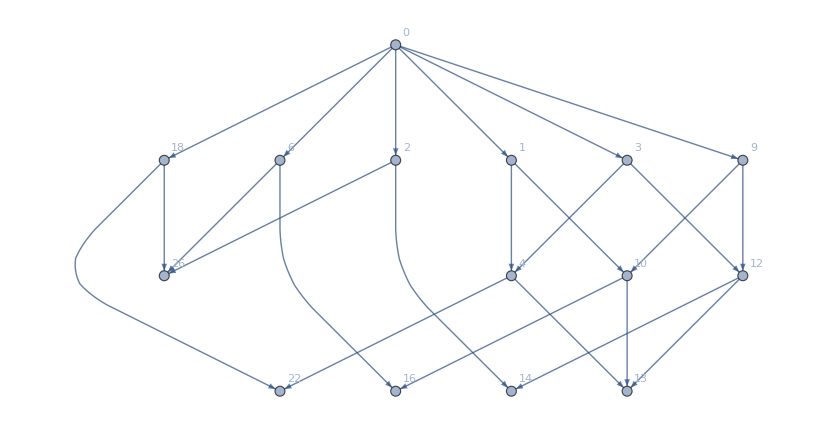

```mathematica
Graph[gCleaned,GraphLayout->"LayeredDigraphEmbedding",VertexLabels->Table[k->With[{g=allGraphs3[k,"graph"]},
Labeled[If[EdgeCount[g]==0,Framed[g],g],Style[k,Blue]]
],{k,fiveSorted}]]
```